```mathematica
(*Import*)
market=Import[FileNameJoin[{verificationDirectory,"market-result.wxf"}],"WXF"];
Get[FileNameJoin[{verificationDirectory,"generator-definition.wl"}]];

(*Mechanical Verification*)
ClearAll["Global`*"];
verificationDirectory=SystemDialogInput["Directory"];
If[verificationDirectory===$Canceled,Abort[]];
market=Import[FileNameJoin[{verificationDirectory,"market-result.wxf"}],"WXF"];
metadata=Import[FileNameJoin[{verificationDirectory,"metadata.json"}],"RawJSON"];
savedHashes=Import[FileNameJoin[{verificationDirectory,"sha256.json"}],"RawJSON"];
parameters=metadata["Parameters"];

(*Verification File Integrity*)
hashResults=Association@KeyValueMap[Function[{savedPath,expectedHash},Module[{localPath,actualHash},localPath=FileNameJoin[{verificationDirectory,FileNameTake[savedPath]}];
actualHash=If[FileExistsQ[localPath],IntegerString[FileHash[localPath,"SHA256"],16,64],Missing["FileNotFound"]];
FileNameTake[savedPath]-><|"Exists"->FileExistsQ[localPath],"HashMatches"->(actualHash===expectedHash)|>]],savedHashes];
Dataset[hashResults]
```

```mathematica
(*Verifying internal structure and mathematical identities*)
requiredKeys={"Returns","Prices","LogPrices","Volatility","Innovation","LogVolatility","ScaleFields"};
seriesKeys={"Returns","Prices","LogPrices","Volatility","Innovation","LogVolatility"};
returns=market["Returns"];
prices=market["Prices"];
logPrices=market["LogPrices"];
volatility=market["Volatility"];
expectedLogPrices=Log[parameters["InitialPrice"]]+Accumulate[returns];
maxLogPriceError=Max[Abs[logPrices-expectedLogPrices]];
maxPriceError=Max[Abs[prices-Exp[logPrices]]];
verificationReport=<|"RequiredKeysPresent"->ContainsAll[Keys[market],requiredKeys],"SeriesLengthsAgree"->SameQ@@(Length/@Lookup[market,seriesKeys]),"ExpectedLength"->(Length[returns]===parameters["Length"]),"ReturnsAreNumeric"->VectorQ[returns,NumericQ],"PricesArePositive"->AllTrue[prices,#>0&],"VolatilityIsPositive"->AllTrue[volatility,#>0&],"LogPriceIdentityPasses"->maxLogPriceError<10^-10,"PriceIdentityPasses"->maxPriceError<10^-10,"MaximumLogPriceError"->maxLogPriceError,"MaximumPriceError"->maxPriceError,"RealizedAnnualizedVolatility"->StandardDeviation[returns] Sqrt[252.],"TotalLogReturn"->Total[returns],"FinalPrice"->Last[prices],"EndpointAppearsArtificiallyPinned"->Abs[Total[returns]]<10^-10|>;
Dataset[verificationReport]
```

```mathematica
(*Deterministic Reproducubility*)
Get[FileNameJoin[{verificationDirectory,"generator-definition.wl"}]];
regenerated=generateMarket[parameters["Length"],parameters["Seed"],parameters["Levels"],parameters["Intermittency"],parameters["Persistence"],parameters["AnnualizedVolatility"],parameters["InitialPrice"]];
reproducibilityReport=<|"ReturnsExactlyReproduced"->SameQ[market["Returns"],regenerated["Returns"]],"VolatilityExactlyReproduced"->SameQ[market["Volatility"],regenerated["Volatility"]],"PricesExactlyReproduced"->SameQ[market["Prices"],regenerated["Prices"]]|>;
Dataset[reproducibilityReport]
```

```mathematica
(*Tail Behaviour and Distribution Verification*)
ClearAll[serialCorrelation,aggregateReturns,structureFunction];
returns=market["Returns"];
logPrices=market["LogPrices"];
standardizedReturns=(returns-Mean[returns])/StandardDeviation[returns];
n=Length[returns];
skewness=Skewness[returns];
excessKurtosis=Kurtosis[returns]-3;
jarqueBera=n/6 (skewness^2+excessKurtosis^2/4);
distributionReport=<|"Observations"->n,"MeanReturn"->Mean[returns],"AnnualizedVolatility"->StandardDeviation[returns] Sqrt[252.],"Skewness"->skewness,"ExcessKurtosis"->excessKurtosis,"JarqueBeraStatistic"->jarqueBera,"JarqueBeraPValue"->SurvivalFunction[ChiSquareDistribution[2],jarqueBera]|>;
Dataset[distributionReport]
```

General::munfl: Exp[-908.637] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
(*Comparision of emperical and gaussian tails*)
probabilities={0.001,0.01,0.05,0.50,0.95,0.99,0.999};
tailRows=Transpose[{probabilities,Quantile[standardizedReturns,probabilities],Quantile[NormalDistribution[],probabilities]}];
tailComparison=Map[AssociationThread[{"Probability","GeneratedQuantile","GaussianQuantile"},#]&,tailRows];
Dataset[tailComparison]
```

```mathematica
(*Plotting the distribution*)
distributionPlot=Show[Histogram[standardizedReturns,{0.20},"PDF",PlotRange->{{-8,8},All},Frame->True,FrameLabel->{"Standardized return","Density"},ChartStyle->Directive[Opacity[0.65],Blue]],Plot[PDF[NormalDistribution[],x],{x,-8,8},PlotStyle->{Red,Thick}],ImageSize->Large];
distributionPlot
Export["DistributionExport.png",distributionPlot]
```

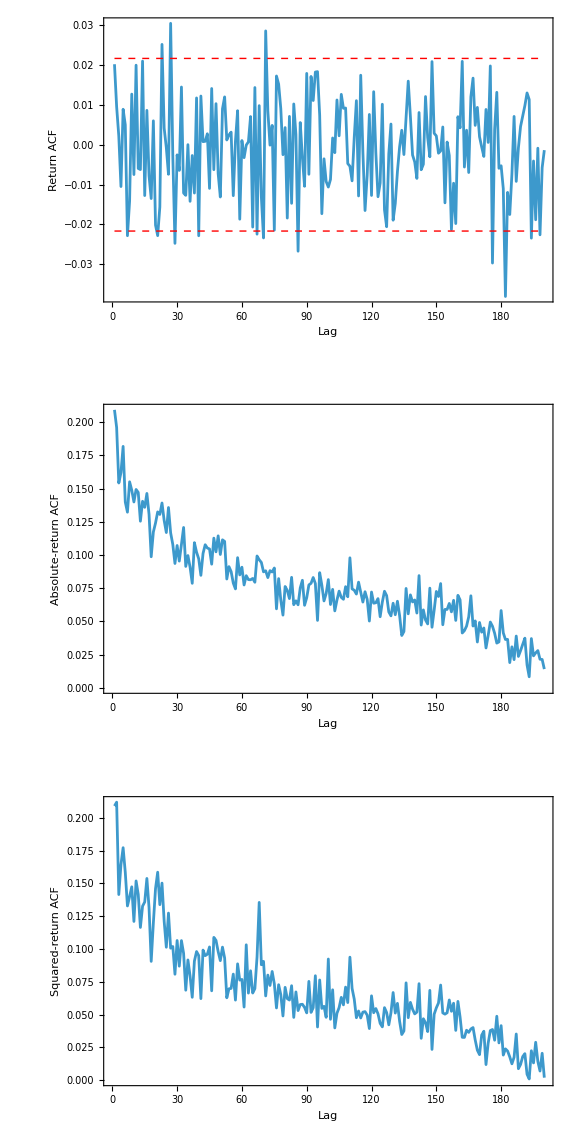

```mathematica
(*Return and volatility autocorrelation*)
serialCorrelation[data_List,maxLag_Integer]:=Table[Correlation[data[[;;-lag-1]],data[[lag+1;;]]],{lag,1,maxLag}];
maxLag=200;
returnACF=serialCorrelation[returns,maxLag];
absoluteReturnACF=serialCorrelation[Abs[returns],maxLag];
squaredReturnACF=serialCorrelation[returns^2,maxLag];
confidenceBand=1.96/Sqrt[n];
acfPlot=GraphicsGrid[{{ListLinePlot[returnACF,Frame->True,PlotRange->All,FrameLabel->{"Lag","Return ACF"},Epilog->{Red,Dashed,Line[{{1,confidenceBand},{maxLag,confidenceBand}}],Line[{{1,-confidenceBand},{maxLag,-confidenceBand}}]}]},{ListLinePlot[absoluteReturnACF,Frame->True,PlotRange->All,FrameLabel->{"Lag","Absolute-return ACF"}]},{ListLinePlot[squaredReturnACF,Frame->True,PlotRange->All,FrameLabel->{"Lag","Squared-return ACF"}]}},ImageSize->Large];
acfPlot
```

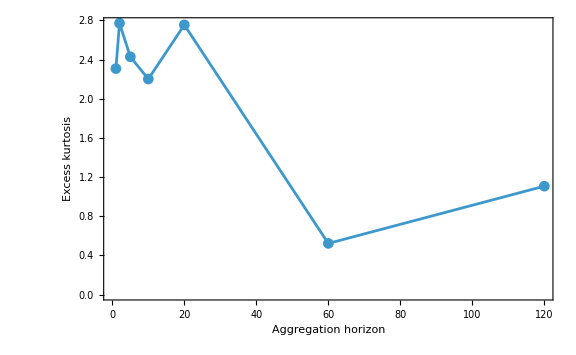

```mathematica
(*Temporal Aggregation*)
aggregateReturns[data_List,horizon_Integer]:=Total/@Partition[data,horizon];
horizons={1,2,5,10,20,60,120};
aggregationStatistics=Table[Module[{aggregated},aggregated=aggregateReturns[returns,horizon];
<|"Horizon"->horizon,"Observations"->Length[aggregated],"Skewness"->Skewness[aggregated],"ExcessKurtosis"->Kurtosis[aggregated]-3|>],{horizon,horizons}];
Dataset[aggregationStatistics]
aggregationPlot=ListLinePlot[{{#["Horizon"],#["ExcessKurtosis"]}&/@aggregationStatistics},Frame->True,FrameLabel->{"Aggregation horizon","Excess kurtosis"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large];
aggregationPlot
```

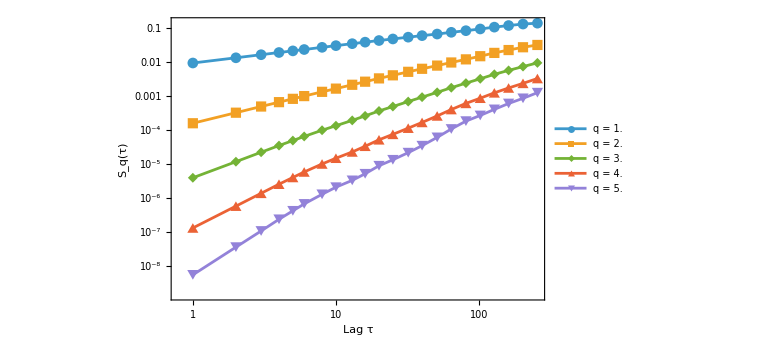

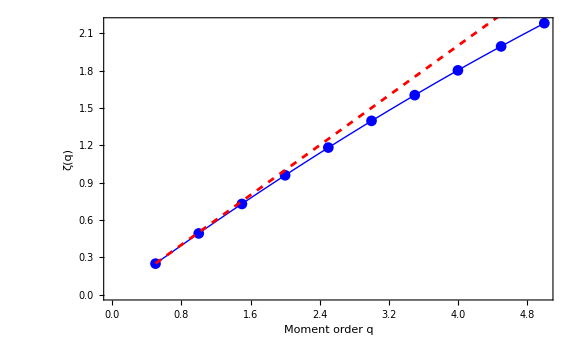

```mathematica
(*Structure functional and scaling exponents*)
structureFunction[data_List,order_?NumericQ,lagValues_List]:=Table[{lag,Mean[Abs[data[[lag+1;;]]-data[[;;-lag-1]]]^order]},{lag,lagValues}];
lags=DeleteDuplicates@Round@Exp@Subdivide[Log[1],Log[256],24];
orders=Range[0.5,5.0,0.5];
scalingResults=Table[Module[{values,fit},values=structureFunction[logPrices,order,lags];
fit=LinearModelFit[Log[values],scaleVariable,scaleVariable];
<|"Order"->order,"Zeta"->Coefficient[Normal[fit],scaleVariable],"RSquared"->fit["RSquared"]|>],{order,orders}];
Dataset[scalingResults]
selectedOrders={1.,2.,3.,4.,5.};
structurePlot=ListLogLogPlot[structureFunction[logPrices,#,lags]&/@selectedOrders,Joined->True,PlotMarkers->Automatic,PlotLegends->("q = "<>ToString[#]&/@selectedOrders),Frame->True,FrameLabel->{"Lag τ","\!\(\*SubscriptBox[\(S\), \(q\)]\)(τ)"},ImageSize->Large];
structurePlot
zetaData={#["Order"],#["Zeta"]}&/@scalingResults;
zetaFit=LinearModelFit[zetaData,{1,q,q^2},q];
zetaCurvature=Coefficient[Normal[zetaFit],q,2];
zetaPlot=Show[ListPlot[zetaData,PlotStyle->Blue,PlotMarkers->Automatic],Plot[Evaluate[Normal[zetaFit]],{q,Min[orders],Max[orders]},PlotStyle->{Blue,Thick}],Plot[q/2,{q,Min[orders],Max[orders]},PlotStyle->{Red,Dashed}],Frame->True,FrameLabel->{"Moment order q","ζ(q)"},ImageSize->Large];
zetaPlot
```

```mathematica
(*Saving Verification Results*)
verificationSummary=<|"Distribution"->distributionReport,"TailComparison"->tailComparison,"Aggregation"->aggregationStatistics,"ScalingExponents"->scalingResults,"ZetaCurvature"->zetaCurvature,"MaximumAbsoluteReturnACFFirst20Lags"->Max[Abs[Take[returnACF,20]]],"MeanAbsoluteReturnACFFirst20Lags"->Mean[Take[absoluteReturnACF,20]],"MeanSquaredReturnACFFirst20Lags"->Mean[Take[squaredReturnACF,20]]|>;
Export[FileNameJoin[{verificationDirectory,"statistical-verification.wxf"}],verificationSummary,"WXF"];
Export[FileNameJoin[{verificationDirectory,"statistical-verification.pdf"}],GraphicsColumn[{distributionPlot,acfPlot,aggregationPlot,structurePlot,zetaPlot}]];
Dataset[verificationSummary]
```

```mathematica
Dataset[verificationSummary["TailComparison"]]
Dataset[verificationSummary["Aggregation"]]
Dataset[verificationSummary["ScalingExponents"]]
```

```mathematica
_□
```